# Stabilized n-Link Pendulum

MonthName Day, Year

Technical Communication & Strategy

we looked at how to model a stabilized inverted pendulum using the control systems design features in Mathematica 8 and 9. We were quickly able to simulate a linearly controlled cart-and-pendulum system, and show that it is stable against some fairly large perturbations.

But what about a double (or triple or quadruple... ) pendulum? A general n-link pendulum is depicted below. In this post we’ll see how to derive the equations of motions for this system, find out whether we can stabilize it with a linear control scheme, and produce some animations of the results.

-Graphics-

For the single pendulum case from the previous post we derived the equations of motion manually, but for the n-link case it is much easier to derive them programmatically. I’ll show one way to do this step by step, using a Lagrangian mechanics formulation. If you prefer, you could easily skip ahead from here to the control theory portion of the post.

The n+1 generalized coordinates describing the n-link pendulum depicted above are the cart position x(t) and the angles of each arm θ_i(t):

```mathematica
coordinates[n_]:=Prepend[Table[Subscript[θ, i][t],{i,n}],x[t]]
```

The n+1 generalized velocities are the time derivatives of the coordinates:

```mathematica
velocities[n_]:=D[coordinates[n],t]
```

Together these comprise the dynamical variables of the n-link pendulum. For the double (“2-link”) pendulum, for example, the dynamical variables are:

```mathematica
Join[coordinates[2],velocities[2]]
```

{x[t],θ_1[t],θ_2[t],x'[t],θ_1'[t],θ_2'[t]}

The n+1 generalized external forces are just the control force f(t) acting on the cart and zero forces acting on each of the other n generalized coordinates:

```mathematica
forces[n_]:=PadRight[{f[t]},n+1,0]
```

For example, the generalized external forces acting on the triple pendulum are:

```mathematica
forces[3]
```

{f[t],0,0,0}

Now we need to compute the Lagrangian of the n-link pendulum. It helps to define a couple of other properties of the system first, starting with the location of the hinge of each of the n arms. The hinge of the first arm is at the horizontal position of the cart, with a height of zero:

```mathematica
hinge[1]={x[t],0};
```

The location of the hinge of each other arm depends on the location of the previous hinge in the following simple way:

```mathematica
hinge[i_]:=hinge[i-1]+Subscript[d, i-1]{Cos[Subscript[θ, i-1][t]],Sin[Subscript[θ, i-1][t]]}
```

For example, the hinge of the second arm is at the end of the first arm:

```mathematica
hinge[2]
```

{Cos[θ_1[t]] d_1+x[t],Sin[θ_1[t]] d_1}

We assume the arms have uniform linear density, so the center of mass of the ith arm is halfway along it:

```mathematica
armcenter[i_]:=hinge[i]+Subscript[d, i]/2{Cos[Subscript[θ, i][t]],Sin[Subscript[θ, i][t]]}
```

The kinetic energy of the ith arm is 1/2 m_i v.v, where v is the velocity of its center of mass:

```mathematica
ke[i_]:=With[{v=D[armcenter[i],t]},1/2 Subscript[m, i] v.v]
```

In our dimensionless units in which the gravitational acceleration g==1, the potential energy of the ith arm is its mass multiplied by the height of its center of mass:

```mathematica
pe[i_]:=Subscript[m, i] armcenter[i]⟦2⟧
```

(The ⟦2⟧ gives the second component of armcenter[i], which is the height.)

The Lagrangian of the cart is just its kinetic energy, c (x'(t))^2/2, so the overall Lagrangian of the n-link pendulum is:

```mathematica
lagrangian[n_]:=1/2 c x'[t]^2+Sum[ke[i]-pe[i],{i,n}]
```

Now we are ready to apply the Euler–Lagrange equations and get the equations of motion:

```mathematica
equations[n_]:=MapThread[{q,v,h}↦
D[D[lagrangian[n],v],t]-D[lagrangian[n],q]==h,{coordinates[n],velocities[n],forces[n]}]
```

(The MapThread function gives the Euler–Lagrange equation, ∂/(∂t)(∂L)/(∂v)-(∂L)/(∂q)==h, for each corresponding generalized coordinate q, generalized velocity v, and generalized force h.)

OK! After a bit of work, we have the equations of motion for any n-link pendulum. Let’s take a look at a few of them.

For n==0 (a cart without any pendulum), we just get Newton’s second law relating the cart’s mass c and acceleration x''(t) to the control force f(t):

```mathematica
equations[0]
```

{c x''[t]==f[t]}

So far, so good. For n==1 we get the same equations of motion as we used in the first post in this series:

```mathematica
equations[1]//Simplify
```

{2 f[t]+d_1 m_1 (Cos[θ_1[t]] θ_1'[t]^2+Sin[θ_1[t]] θ_1''[t])==2 (c+m_1) x''[t],d_1 m_1 (2 Cos[θ_1[t]]-2 Sin[θ_1[t]] x''[t]+d_1 θ_1''[t])==0}

For n==2, a cart-and-double-pendulum system, the explicit equations of motion are fairly complicated:

```mathematica
equations[2]//Simplify
```

{(c+m_1+m_2) x''[t]==f[t]+1/2 (d_1 (m_1+2 m_2) (Cos[θ_1[t]] θ_1'[t]^2+Sin[θ_1[t]] θ_1''[t])+d_2 m_2 (Cos[θ_2[t]] θ_2'[t]^2+Sin[θ_2[t]] θ_2''[t])),d_1 (m_1 (2 Cos[θ_1[t]]-2 Sin[θ_1[t]] x''[t]+d_1 θ_1''[t])+2 m_2 (2 (Cos[θ_1[t]]-Sin[θ_1[t]] x''[t]+d_1 θ_1''[t])+d_2 (Sin[θ_1[t]-θ_2[t]] θ_2'[t]^2+Cos[θ_1[t]-θ_2[t]] θ_2''[t])))==0,d_2 m_2 (2 Cos[θ_2[t]]-2 Sin[θ_2[t]] x''[t]+2 d_1 (-Sin[θ_1[t]-θ_2[t]] θ_1'[t]^2+Cos[θ_1[t]-θ_2[t]] θ_1''[t])+d_2 θ_2''[t])==0}

The equations become much longer for larger n, but we will happily use them without ever looking at them.

(If you do want to see the equations of motion for, say, a quadruple pendulum printed out in full, just download the notebook for this post and evaluate  equations[4]. The output is about five pages long on-screen, which is exactly why you don’t want to derive these things by hand.)

We used symbolic math and programming to set up the equations of motion. Now we can immediately use Mathematica’s numerics and control systems features to simulate and stabilize them. This is what’s great about having all these areas integrated into one system!

We'll investigate the concrete case c==m_i==d_i==1:

```mathematica
parameters={c->1,Subscript[m, i_]->1,Subscript[d, i_]->1};
```

(The m_i_ means “m_i for all values of i”.)

It’s handy to define a function initial[n] that generates some slightly non-upright initial conditions at t==0 for an n-link pendulum. For example, here are slightly non-upright initial conditions for a single pendulum:

```mathematica
initial[1]
```

{x[0]==x'[0]==0,θ_1[0]==1.50009,θ_1'[0]==0}

Note that the pendulum is exactly upright when each θ_i==π/2≃1.5708. (Download the notebook to see the definition of initial[n], or to substitute your own.)

We’ll start by simulating a double pendulum with no control force, f(t)==0, corresponding to making no attempt to balance the pendulum:

```mathematica
NDSolve[Join[equations[2],initial[2]]/.parameters/.f[t]->0,coordinates[2],{t,0,15}]
```

{{x[t]→InterpolatingFunction[{{0.,15.}},<>][t],θ_1[t]→InterpolatingFunction[{{0.,15.}},<>][t],θ_2[t]→InterpolatingFunction[{{0.,15.}},<>][t]}}

Here’s an animation of the solution:

```mathematica
AnimateNPendulum[First[%]]
```

(As in the previous post, you can see the definition of the function AnimateNPendulum by downloading the notebook.)

Once again, it’s convenient to combine the above steps into a single function:

```mathematica
SimulateNPendulum[n_,force_]:=AnimateNPendulum[First[NDSolve[Join[equations[n],initial[n]]/.parameters/.f[t]->force,coordinates[n],{t,0,25}]]]
```

Using this function, here’s a triple pendulum falling over, with no attempt to control it:

```mathematica
SimulateNPendulum[3,0]
```

It gets messy fast, but we’ll be able to steady it!

First, we need a state space model of the n-link pendulum, linearized around the equilibrium point. The function StateSpaceModel automatically generates this for us from our nonlinear equations of motion:

```mathematica
model[n_]:=StateSpaceModel[equations[n]/.parameters,equilibrium[n],f[t],{},t]
```

The function equilibrium[n] just gives the unstable (upright) equilibrium point for an n-link pendulum: θ_i==π/2; everything else==0. For example, for a double pendulum:

```mathematica
equilibrium[2]
```

{{x[t],0},{x'[t],0},{θ_1[t],π/2},{θ_1'[t],0},{θ_2[t],π/2},{θ_2'[t],0}}

(Download the notebook to see the definition of equilibrium[n].)

Here is the linearized state space model for our double pendulum:

```mathematica
model[2]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 12 | 0 | -6 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -18 | 0 | 12 | 0 | -2)_^𝒮

each column in this augmented matrix describes the immediate effect of one of the dynamical variables (or the control force) on each of the other dynamical variables.

We can now compute a linear control force for this system. For a double pendulum, for example, the linear control force will have the form

f(t)==k_1 x(t)+k_2 x'(t)+k_3 (θ_1(t)-π/2)+k_4 θ_1'(t)+k_5 (θ_2(t)-π/2)+k_6 θ_2'(t).

LQRegulatorGains gives values for the feedback gains k_i:

```mathematica
LQRegulatorGains[N[model[2]],{DiagonalMatrix[{10,20,100,1000,100,1000}],{{1}}}]//First
```

{3.16228,19.8336,79.8048,-31.6649,-135.84,-68.8886}

As discussed in the previous post, the second argument to LQRegulatorGains specifies a quadratic cost function whose integral over time is minimized (in the linearized model). The exact cost function specified above is

∫_0^∞ (10 (x(t))^2+20 (x'(t))^2+100 (θ_1(t))^2+1000 (θ_1'(t))^2+100 (θ_2(t))^2+1000 (θ_2'(t))^2+(f(t))^2)ⅆt.

The coefficients in the quadratic cost function may represent actual costs of deviations of the system from the desired equilibrium state, or they may be chosen according to other criteria, such as robustness against certain types of perturbations. The cost coefficients I’ve used here are a guess, based on which dynamical variables I suspect are the most important for keeping the pendulum from falling over.

Here is a generalization of my guessed cost coefficients to an n-link pendulum:

```mathematica
costs[n_]:=DiagonalMatrix[PadRight[{10,20},2n+2,{100,1000}]]
```

The corresponding feedback gains are:

```mathematica
gains[n_]:=First@LQRegulatorGains[N[model[n]],{costs[n],{{1}}}];
```

And the control force is:

```mathematica
controlforce[n_]:=-gains[n].(Subtract@@@equilibrium[n])
```

Our control force for a double pendulum is:

```mathematica
controlforce[2]
```

-3.16228 x[t]-79.8048 (-π/2+θ_1[t])+135.84 (-π/2+θ_2[t])-19.8336 x'[t]+31.6649 θ_1'[t]+68.8886 θ_2'[t]

How well does it work?

```mathematica
SimulateNPendulum[2,controlforce[2]]
```

Very graceful! Here’s the stabilized triple pendulum (compare it to the freely falling triple pendulum above):

```mathematica
SimulateNPendulum[3,controlforce[3]]
```

Some pretty nifty maneuvering is needed to catch the quadruple pendulum before it falls over:

```mathematica
SimulateNPendulum[4,controlforce[4]]
```

Let’s see what sort of bumping around the double pendulum can handle. We’ll apply generalized forces h_1(t) and h_2(t) to the coordinates θ_1(t) and θ_2(t) respectively. (We are effectively applying torques to the first and second hinges of the pendulum.)

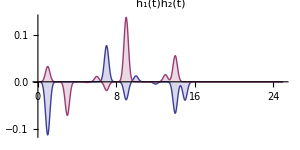

```mathematica
Plot[{Subscript[h, 1][t],Subscript[h, 2][t]},{t,0,25},PlotRange->All,ImageSize->300,Filling->Axis,PlotLabel->Row[{Style[HoldForm@Subscript[h, 1][t],ColorData[1][1]],Style[HoldForm@Subscript[h, 2][t],ColorData[1][2]]},","],AxesLabel->{t},AspectRatio->1/2]
```

(Download the notebook to see the definitions of h_1(t) and h_2(t) , or to substitute your own.)

Here’s the bumped double pendulum:

```mathematica
Block[{forces,SimulateNPendulum},
forces[2]={f[t],Subscript[h, 1][t],Subscript[h, 2][t]};
SimulateNPendulum[n_,force_]:=AnimateNPendulum[First[NDSolve[Join[equations[n],initial[n]]/.parameters/.f[t]->force,coordinates[n],{t,0,35}]]];SimulateNPendulum[2,controlforce[2]]
]
```

It’s also interesting to directly plot the generalized coordinates x(t), θ_1(t), and θ_2(t), and compare with the forces  h_1(t) and h_2(t) and the control force f(t):

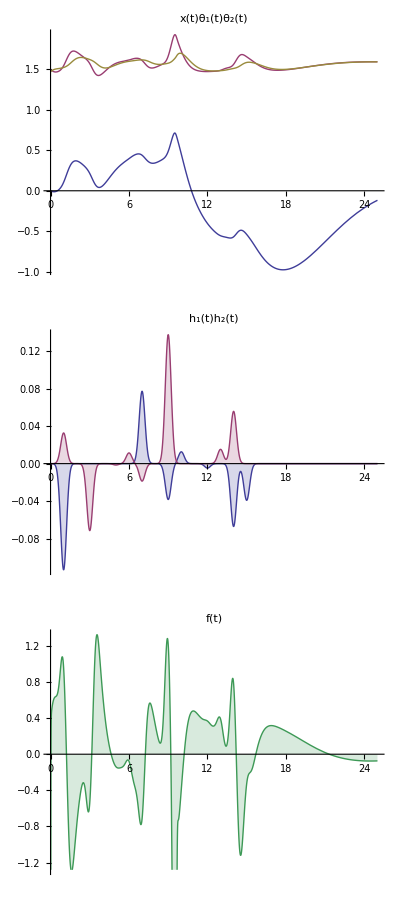

```mathematica
Block[{forces,sol},
forces[2]={f[t],Subscript[h, 1][t],Subscript[h, 2][t]};
sol=First[NDSolve[Join[equations[2],initial[2]]/.parameters/.f[t]->controlforce[2],Head/@coordinates[2],{t,0,35}]];Column[{
Plot[Evaluate[coordinates[2]/.sol],{t,0,25},ImagePadding->{{20,15},{Automatic,Automatic}},PlotLabel->Row[MapThread[Style[##,12]&,{coordinates[2],ColorData[1]/@Range[3]}],","],ImageSize->300,AxesLabel->{t}],Plot[{Subscript[h, 1][t],Subscript[h, 2][t]},{t,0,25},PlotRange->All,ImageSize->300,Filling->Axis,AspectRatio->1/3,PlotLabel->Row[{Style[HoldForm@Subscript[h, 1][t],ColorData[1][1]],Style[HoldForm@Subscript[h, 2][t],ColorData[1][2]]},","],AxesLabel->{t},Ticks->{Automatic,Automatic},ImagePadding->{{20,15},{Automatic,Automatic}}],Plot[Evaluate[PadLeft[{controlforce[2]},4,"dummy"]/.sol],{t,0,25},ImagePadding->{{20,15},{Automatic,Automatic}},PlotRange->Automatic,Filling->Automatic,AspectRatio->1/3,ImageSize->300,AxesLabel->{t},PlotLabel->Row[{"",Style[HoldForm@f[t],ColorData[1][4]]}]]}]
]
```

With sufficiently large perturbations, linear control systems such as the ones we have been exploring will fail to recover (and will spiral out of control). Moreover, for n-link pendulums, larger values of n require smaller angular perturbations to knock them over, and in real life there are always perturbations (sound, heat, wind... ). In practice it’s hard to build physical demonstrations of n-link pendulums with more than about three or four links.

Nevertheless, it’s very interesting to explore these idealized systems. There are lots of things you can try with the downloadable notebook for this post. For example, with different choices for the cost function, you can make linear control systems for inverted n-link pendulums that can recover from different (including larger) initial perturbations. Or, with different lengths and masses of the pendulum arms (and no control force), you can explore the dynamics of n-link pendulums, which are very interesting by themselves. Try it out!

In the next post in this series, we’ll look at some more generalizations and variations on this problem, including inverted pendulums in 3D.

## Supplementary notes

Here’s a version of SimulatePendulum[n,force] that is more robust for n-link pendulums with larger values of n:

```mathematica
SimulateNPendulum[n_,force_]:=AnimateNPendulum[First[NDSolve[Join[equations[n],initial[n]]/.parameters/.f[t]->force,coordinates[n],{t,0,25},SolveDelayed->True,MaxSteps->∞]]]
```

(The option SolvedDelayed→True tells NDSolve not to try to symbolically solve the differential equations for the various derivatives—this can take a long time for large values of n. Instead, the equations are solved numerically at each time step.)

## AnimateNPendulum

Check whether a solution from NDSolve appears to keep the pendulum upright, by checking that the height of every hinge appears to stay above y==0:

```mathematica
NPendulumAppearsStableQ[rules_,parameterrules_]:=Block[{n=Length[rules]-1,maxt=Max[First[Head[x[t]/.rules]]],expr},expr=Table[Last[hinge[i]],{i,2,n+1}]/Accumulate[Table[Subscript[d, i],{i,n}]]/.parameters/.rules;Min[Map[Min[expr]/.t->#&,RandomReal[{0,maxt},100]]]>0]
```

Farthest the cart gets from the origin:

```mathematica
NPendulumCartXMaximum[rules_]:=Block[{maxt=Max[First[Head[x[t]/.rules]]]},Max@Abs@Map[x[t]/.rules/.t->#&,RandomReal[{0,maxt},100]]]
```

```mathematica
NPendulumCartXMaximum[rules_]:=Block[{maxt=Max[First[Head[x[t]/.rules]]]},Abs@First@NMaximize[{x[t]/.rules,0<t<maxt},t,PrecisionGoal->2]]
```

Animate a solution from NDSolve using a plot range style determined by whether the pendulum appears to be upright and stable:

```mathematica
AnimateNPendulum[rules_,parameterrules_:Automatic]:=Animate[Evaluate[DrawNPendulum[rules,parameterrules/.Automatic->parameters,t,If[NPendulumAppearsStableQ[rules,parameterrules],"Stable","Fixed"],NPendulumCartXMaximum[rules]]],{t,0,Max[First[Head[x[t]/.rules]]]},DefaultDuration->15,AnimationRunning->False]
```

Draw an n-pendulum at a single instant t==s from raw numerical generalized coordinates and parameters:

```mathematica
$StablePendulumPlotPadding=0.25;
$ArmDensity=30;
DrawNPendulum[angles_List,lengths_List,masses_List,cartx_,s_,type_:Automatic,maxcart_:0]:=
Module[{plotrange,widths,cartgraphics,armgraphics,colors},

(* PlotRange *)
Which[type==="Stable",
Block[{w=Max[Total[lengths]+2$StablePendulumPlotPadding,2(Max[Abs[cartx],maxcart]+$StablePendulumPlotPadding)]},
plotrange={{-w/2,w/2},{-$StablePendulumPlotPadding,w-$StablePendulumPlotPadding}};
];,
type===Automatic,
plotrange=Max[Total[lengths]+$StablePendulumPlotPadding,Total[Most[lengths]+Abs[cartx]]];,
type==="Fixed"||type===True,
plotrange=Total[lengths];
];

colors=ColorData[1]/@Range[2,Length[angles]+1];
colors=PadRight[{},Length[angles],{Orange,Darker[Orange]}];

cartgraphics={ColorData[1][1];Blue,Rectangle[{cartx-0.25,-0.05},{cartx+0.25,0.05}]};

widths=masses/(lengths*$ArmDensity);

Block[{pos={cartx,0},res},
armgraphics=
MapThread[
Function[{angle,length,width,color},
res={color,Translate[Rotate[Rectangle[{0,width},{length,-width}],angle,{0,0}],pos]};
pos+=length{Cos[angle],Sin[angle]};
res
],
{angles,lengths,widths,colors}
];
];

Graphics[{cartgraphics,armgraphics},
PlotRange->plotrange,
Frame->True,
AxesStyle->{Dashed,Dashed},
Axes->{True,True},
ImageSize->280,
AxesOrigin->{0,0},
Epilog->If[type==="Stable",{Dashed,Line[{{0,0},{100,0}}],Line[{{0,0},{-100,0}}]},{}],
PlotLabel->"t"==NumberForm[s,{4,2}]
]
]
```

Draw an n-pendulum at a single instant t==s from rules from NDSolve and parameters:

```mathematica
DrawNPendulum[{variables___Rule},{parameters___Rule},s_,type_:Automatic,maxcart_:0]:=Block[{n=Length[{variables}]-1,angles,lengths,masses,cartx},
angles=Table[Subscript[θ, i][t],{i,n}]/.{variables}/.t->s;
cartx=x[t]/.{variables}/.t->s;
lengths=Table[Subscript[d, i],{i,n}]/.{parameters};
masses=Table[Subscript[m, i],{i,n}]/.{parameters};
DrawNPendulum[angles,lengths,masses,cartx,s,type,maxcart]
]
```

## equilibrium[n]

```mathematica
equilibrium[n_]:=Join[{{x[t],0},{x'[t],0}},Sequence@@Table[{{Subscript[θ, i][t],π/2},{Subscript[θ, i]'[t],0}},{i,n}]]
```

## initial[n]

```mathematica
Clear[initial]
```

```mathematica
initial[n_]:=Flatten[{x[0]==x'[0]==0,Table[{Subscript[θ, i][0]==N[π/2-1/20(√2)^i],Subscript[θ, i]'[0]==0},{i,n}]}]
```

## Bumpy force

```mathematica
(* generate random bumpy conditions *)
Subscript[h, 1][t_]=
verybumpy[t_]=Sum[RandomReal[{-8,8}]/100 Exp[-10(t-RandomInteger[15])^2],{10}];
Subscript[h, 2][t_]=
verybumpy[t_]=Sum[RandomReal[{-8,8}]/100 Exp[-10(t-RandomInteger[15])^2],{10}];
(* used fixed bumpy conditions *)
Subscript[h, 1][t_]=-0.03908137506754105 ⅇ^(-10 (-15+t)^2)-0.06696306905134353 ⅇ^(-10 (-14+t)^2)-0.004742722169292648 ⅇ^(-10 (-12+t)^2)+0.012573439012288504 ⅇ^(-10 (-10+t)^2)-0.03820196550892622 ⅇ^(-10 (-9+t)^2)+0.07705340349752843 ⅇ^(-10 (-7+t)^2)-0.11312872229651061 ⅇ^(-10 (-1+t)^2);
Subscript[h, 2][t_]=0.055660890251393806 ⅇ^(-10 (-14+t)^2)+0.015189848681240044 ⅇ^(-10 (-13+t)^2)+0.13735661430385204 ⅇ^(-10 (-9+t)^2)-0.01861825459824459 ⅇ^(-10 (-7+t)^2)+0.011379177639259766 ⅇ^(-10 (-6+t)^2)-0.0014880711710300032 ⅇ^(-10 (-5+t)^2)-0.07136068018810363 ⅇ^(-10 (-3+t)^2)+0.032641281448719896 ⅇ^(-10 (-1+t)^2);
```